## Numerical

### Constants and Functions

```mathematica
MeV=1;
keV=10^-3 MeV;
eV=10^-6 MeV;
GeV=10^3 MeV;
{Me=0.511 MeV,Gf= (1.16637×10^-5)(*GeV^-2*)×10^-18 eV^-2};
eU1em=√(4π α)/.α->1/137.04;
centimeter=5.06842372022301*^10 MeV^-1;



Clear[sw,A12B12,GpmSM];

(*CCstatus={"on","off"}⟦CCi=1⟧;*)
(*nuMode={"nu","nubar"}⟦nui=1⟧;*)
Clear[σtot];

σpart[En_,{A1_,A2_,B1_,B2_},mZp_,T1_,T2_]:=Module[{X={A1,A2,B1,B2},T1x,T2x,Tmax=(2 En^2)/(Me+2En)},
If[nuMode=="nubar",X={A2,A1,B2,B1}];
If[T1>T2,err[]];

If[(T2<Tmax),T1x=T1;T2x=T2];
If[(T1≤ Tmax≤ T2),T1x=T1;T2x=Tmax];
If[(Tmax<T1),Return[0]];
(X.Iij[{T1x,T2x,En,mZp,Me,Gf}].X)
];





GpmSM[{sw_,cα_}]:={ -2 √2 Gf cα^2  sw^2,√2 Gf (cα^2  (1-2 sw^2)+
(*Which[CCint=="on",-2,CCint=="off",0,True,err[]]*){-2,0}⟦CCi⟧)};

A12B12[{gx_,ϵ_,α_},sw_]:=Module[{cw=√(1-sw^2),g,cα=Cos[α],sα=Sin[α],GpSM,GmSM,A,B,H,G},
g=eU1em/sw;

{GpSM,GmSM}=GpmSM[{sw,cα}];


{H=  (-cw gx QeL-g sw ϵ) (cw gx QνL+g sw ϵ)/(2 (-1+ϵ^2)),
G=   g  (cw gx (QeL-QνL+2 QνL sw^2)+2 g sw^3 ϵ) √(1-ϵ^2)/(2 (-1+ϵ^2))};
{A= 1/(2(1-ϵ^2))(cw^2 gx^2 QeR QνL+cw g gx (QeR+2 QνL) sw ϵ+2 g^2 sw^2 ϵ^2),
B= 1/(2(1-ϵ^2))(-cw g gx (QeR+2 QνL sw^2) √(1-ϵ^2)-2 g^2 sw ϵ √(1-ϵ^2)-2 g^2 sw^3 ϵ √(1-ϵ^2))};



{(*A1=*)GpSM-1/g^2 2 √2 Gf ((*cα^2 g^2 sw^2+*)B cα sα+A sα^2),
(*A2=*)GmSM-1/g^2 2 √2 Gf ((*cα^2 g^2 (-1/2+sw^2)+*)cα G sα+H sα^2),
(*B1=*)-Gf(A cα^2-B cα sα+g^2 sw^2 sα^2)/(2 cw^2 ),
(*B2=*)-Gf(cα^2 H-cα G sα+g^2 (-1/2+sw^2) sα^2)/(2 cw^2 )}
];

computeNs[{mzp_,gx_,ϵ_,α_},sw_]:=Module[{T1,T2},
tbl[
T1=bin⟦1⟧;
T2=bin⟦2⟧;
crossSectionList=Table[σpart[En,A12B12[{gx,ϵ,α},sw],mzp,T1,T2],{En,fluxShapeList⟦1⟧}];
scaleFactor ΔEn(fluxShapeList⟦2⟧.crossSectionList)
,{bin,binList}]
]

setScaleFactor[sw_]:=(
scaleFactor=1;
Ntot=Total[computeNs[{(*mzp*)0,(*gx*)0,(*ϵ*)0,(*α*)0},sw]];
scaleFactor=NtotSM/Ntot;
)

printInfo[]:=(print["CC int.: ",CCstatus,"\n ν/νbar mode: ", nuMode];
print[(*"{EnMin,EnMax}=",{EnMin,EnMax},*)" Tmin=", Tmin,"MeV"];)

setfluxShapeList[EnMin_,EnMax_]:=(If[expName=="GEMMA",nofΔEn=60,nofΔEn=20];fluxShapeList=Table[{En,fluxShape[En]},{En,EnMin,EnMax,ΔEn=(EnMax-EnMin)/nofΔEn}]ᵀ;
)


froot[f_,{x1_,x2_}]:=Module[{xsol},xsol=FindRoot[f[x]==0,{x,x1,x2},Method->"Brent"]⟦1,2⟧;
If[f[(x1+xsol)/2]f[x1]<0,
(*print[Table[{x,f[x]},{x,{x1,(x1+xsol)/2,xsol,(x2+xsol)/2,x2}}]];*)
xsol=FindRoot[f[x]==0,{x,x1,(1x1+1xsol)/2},Method->"Brent"]⟦1,2⟧];

If[f[(x1+xsol)/2]f[x1]<0,
(*print[Table[{x,f[x]},{x,{x1,(x1+xsol)/2,xsol,(x2+xsol)/2,x2}}]];*)err[]];

xsol
]

chi2[y_,y0_,d_]:=Total[((y-y0)/d)^2]
```

### CHARM II

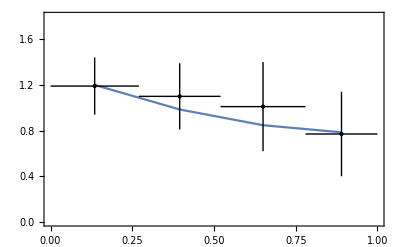

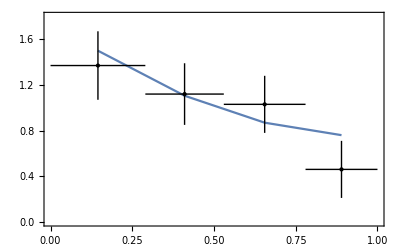

{1.19,1.1,1.01,0.77,1.37,1.12,1.03,0.46}

{1.2,0.985047,0.847227,0.784789,1.5,1.10549,0.869321,0.759992}

{0.25,0.29,0.39,0.37,0.3,0.27,0.25,0.25}

```mathematica
swCHARMII=√0.23;
computeσinBins[{mZp_,gx_,ϵ_,α_},sw_]:=Module[{En},
nuMode={"nu","nubar"}⟦nui=1⟧;
En=20GeV;
σinBins=scalefactor tbl[σpart[En,A12B12[{gx,ϵ,α},sw],mZp,Mean[y12] En,(Mean[y12]+0.001) En]
,{y12,ybins}];


nuMode={"nu","nubar"}⟦nui=2⟧;
En=20GeV;σinBinsB=scalefactorB tbl[σpart[En,A12B12[{gx,ϵ,α},sw],mZp,Mean[y12] En,(Mean[y12]+0.001) En]
,{y12,ybinsB}];
{σinBins,σinBinsB}

]


ybins={{0,0.27},{0.27,0.52},{0.52,0.78},{0.78,1.00}};
ybinsMid=Mean[ybinsᵀ];
dσdyData={1.19,1.10,1.01,0.77};
dσdyErr={0.25,0.29,0.39,0.37};

ybinsB={{0,0.29},{0.29,0.53},{0.53,0.78},{0.78,1.00}};
ybinsMidB=Mean[ybinsBᵀ];
dσdyDataB={1.37,1.12,1.03,0.46};
dσdyErrB={0.30,0.27,0.25,0.25};


Clear[datagraph]
datagraph[ybins_,ybinsMid_,dσdyData_,dσdyErr_]:=Graphics[{{PointSize[Large],Point[{ybinsMid,dσdyData}ᵀ]},Table[{Line[{{ybinsMid⟦i⟧,dσdyData⟦i⟧+dσdyErr⟦i⟧},{ybinsMid⟦i⟧,dσdyData⟦i⟧-dσdyErr⟦i⟧}}],Line[{{ybins⟦i,1⟧,dσdyData⟦i⟧},{ybins⟦i,2⟧,dσdyData⟦i⟧}}]},{i,Length[ybins]}]
}];


setCHARM[]:=Module[{},
expName="CHARM";
CCstatus={"on","off"}⟦CCi=2⟧;

scalefactor=1;
scalefactorB=1;
computeσinBins[{0,0,0,0},swCHARMII];
scalefactor=1.2/σinBins⟦1⟧;
scalefactorB=1.5/σinBinsB⟦1⟧;
]


setCHARM[]

{σinBins,σinBinsB}=computeσinBins[{0,0,0,0},swCHARMII];

Show[{ListPlot[{ybinsMid, σinBins}ᵀ,Joined->True],datagraph[ybins,ybinsMid,dσdyData,dσdyErr]
},PlotRange->{0,1.8},Frame->True,Axes->False]
Show[{
ListPlot[{ybinsMidB, σinBinsB}ᵀ,Joined->True],datagraph[ybinsB,ybinsMidB,dσdyDataB,dσdyErrB]
},PlotRange->{0,1.8},Frame->True,Axes->False]

NsObs=Join[dσdyData,dσdyDataB]
NSM=Flatten[computeσinBins[{0,0,0,0},swCHARMII]]
ΔNsObs=Join[dσdyErr,dσdyErrB]
```

```mathematica
chi20=Total[((NSM-NsObs)/ΔNsObs)^2]
(*the SM of χ^2*)
```

2.37819

```mathematica
(*F0123 should be a function like 
F0123={mzp,#,0,0}&, F0123={mzp,0.2#,0.4#,0}&, etc.
output of F0123 is
{mZp,gx,ϵ,α}
*)

find′bound[F0123_,range_:{0,1}]:=froot[(Total[((Flatten[computeσinBins[F0123[#],swCHARMII]]-NsObs)/ΔNsObs)^2]-chi20-sig^2)&,range];
```

```mathematica
sig=√2.71;
mzplist=10^Range[-4.0,4.0,0.1] GeV;
(*For bounds on θ, Q is irrelevant*)
QeR=-1;
QνL= QeL=-1;
θboundsCHARM=Table[{mzp/MeV,
find′bound[{mzp,0,0,#}&] 
}//Log10,{mzp,1.0mzplist}];//Timing
```

{4.53043,Null}

```mathematica
mz=91.19GeV;
mzplist=Join[10^Range[-4.0,1.0,0.1],10^Range[1.1,3,0.02]] GeV;
ϵboundsCHARM=Table[{mzp/MeV,
find′bound[
{mzp,0,#,ArcTan[# sw/(rm-1)/.{sw->swCHARMII,rm->(mzp/mz)^2}]}&
,{0,0.99}] 
}//Log10,{mzp,1.0mzplist}];//Timing
```

{9.73883,Null}

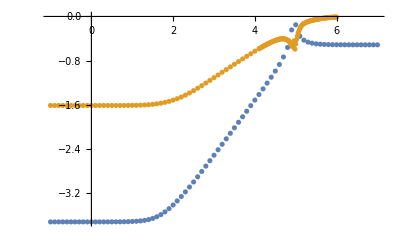

```mathematica
ListPlot[{θboundsCHARM,ϵboundsCHARM}]
```

```mathematica
(*θboundsCHARM*)
Export["data/CHARMII_theta.dat",θboundsCHARM]
Export["data/CHARMII_epsilon.dat",ϵboundsCHARM]
```

data/CHARMII_theta.dat

data/CHARMII_epsilon.dat

```mathematica
sig=√2.71;
mzplist=10^Range[-4.0,3.5,0.1] GeV;

(*For bounds on g, we need to specify Q *)
QeR=0;
QνL= QeL=-1;
gboundsCHARM=Table[{mzp/MeV,
find′bound[{mzp,#,0,0}&,{0,4π}]
}//Log10,{mzp,1.0mzplist}];//Timing
(*Export["data/CHARMII_gU1L.dat",gboundsCHARM]*)


QeR=-1;
QνL= QeL=-3/2;
gboundsCHARM=Table[{mzp/MeV,
find′bound[{mzp,#,0,0}&,{0,4π}]
}//Log10,{mzp,1.0mzplist}];//Timing
(*Export["data/CHARMII_gU1X.dat",gboundsCHARM]*)
```

{4.11331,Null}

{4.05392,Null}

data/CHARMII_gU1X.dat

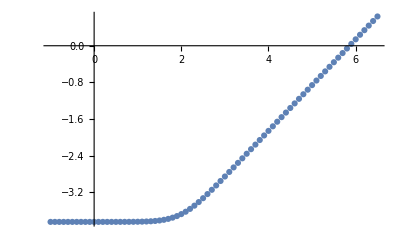

```mathematica
gboundsCHARM//ListPlot
```

```mathematica
(*Bounds on sθ with g={0.01,1,10}sθ, B-L*)
mzplist=10^Range[-4.0,4,0.1] GeV;
QeR=-1;
QνL= QeL=-1;
sθgboundsCHARM=Table[{mzp/MeV,
find′bound[{mzp,0.01#,0,#}&,{0,1}],
find′bound[{mzp,1.0#,0,#}&,{0,1}],
find′bound[{mzp,10.0#,0,#}&,{0,1}]
}//Log10,{mzp,1.0mzplist}];//Timing
```

{13.2728,Null}

```mathematica
Export["data/CHARMII_theta_B_L.dat",sθgboundsCHARM]
```

data/CHARMII_theta_B_L.dat

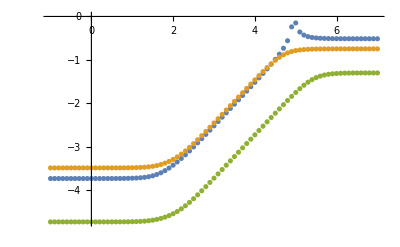

```mathematica
ListPlot[{sθgboundsCHARM⟦All,{1,2}⟧,sθgboundsCHARM⟦All,{1,3}⟧,sθgboundsCHARM⟦All,{1,4}⟧}]
```

### TEXNON

0911.1597
3.0<Eν<8.0 
3.0<T<8.0

```mathematica
swTEXONO=√0.238;
TEXONOSM=Import["data/Texono/TEXONO-R-SM.csv"]⟦All,2⟧;TEXONOdata=Import["data/Texono/TEXONO-R-data.csv"]⟦All,2⟧;TEXONOerror=Import["data/Texono/TEXONO-R-errorU.csv"]⟦All,2⟧;
TEXONOerror=TEXONOerror-TEXONOdata;
```

```mathematica
setTEXONO[]:=Module[{sw, EnMin,EnMax,EnMean,ΔT},
expName="TEXONO";
CCstatus={"on","off"}⟦CCi=1⟧;
nuMode={"nu","nubar"}⟦nui=2⟧;

(*set flux*)
lgrawdata = Import["data/Texono/texono-flux.csv"];
lgϕraw=Interpolation[lgrawdata,InterpolationOrder->1];
fluxShape[En_]:=10^lgϕraw[En];
{EnMin,EnMax}={3,8.0}MeV;

Tmin=3 MeV;
Clear[T2cut(*,Tmin*)];

ΔT=0.5MeV;
binleft=Module[{},Table[T,{T,Tmin,7.5MeV,ΔT}]];
binright=binleft+ΔT;
binList={binleft,binright}ᵀ;


(*set up fluxShapeList and ΔEn*)
(*fluxShapeList={{Eν1,Eν2,...},{ϕ1,ϕ2,...}}*)
setfluxShapeList[EnMin,EnMax];

printInfo[];


swShould=swTEXONO;
NtotSM=Total[TEXONOSM];
setScaleFactor[swShould]
];
```

```mathematica
(*a necessary test*)
QeR=-1;
QνL= QeL=-1;
setTEXONO[];
computeNs[(*{mzp_,gx_,ϵ_,α_}*){0,0,0,0},swTEXONO]
```

CC int.: on
 ν/νbar mode: nubar

Tmin=3MeV

{0.0123009,0.00660248,0.00347477,0.00178742,0.000892009,0.000427728,0.000192871,0.0000812098,0.0000290555,4.22854×10^-6}

```mathematica
NsObs=TEXONOdata
ΔNsObs=TEXONOerror
```

{0.012439,0.00545732,0.00439024,0.00405488,0.00286585,-0.000426829,0.00158537,-0.00070122,-0.00137195,0.00118902}

{0.00387195,0.00240854,0.00195122,0.00164634,0.0014939,0.00125,0.00118902,0.00128049,0.00121951,0.00118902}

```mathematica
chi2[para_]:=Total[((computeNs[para,swShould]-NsObs)/ΔNsObs)^2];
chi20=chi2[{0,0,0,0}]
```

8.61507

```mathematica
mzplist=10^Range[-3,1,0.2] GeV;
QeR=-1;
QνL= QeL=-1;
sig=√2.71;
θboundsTEXONO=Table[mzpout=mzp;{mzp/MeV,
froot[(chi2[{mzp,0,0,#}]-chi20-sig^2)&,{0,1}]}//Log10,{mzp,1.0mzplist}];//Timing
```

{20.7004,Null}

```mathematica
mz=91.19GeV;
ϵboundsTEXONO=Table[mzpout=mzp;{mzp/MeV,
froot[(chi2[{mzp,0,#,ArcTan[# sw/(rm-1)/.{sw->swTEXONO,rm->(mzp/mz)^2}]}]-chi20-sig^2)&,
{0,0.99}]}//Log10,{mzp,1.0mzplist}];//Timing
```

{25.0328,Null}

```mathematica
(*ϵboundsTEXONO//ListPlot*)
```

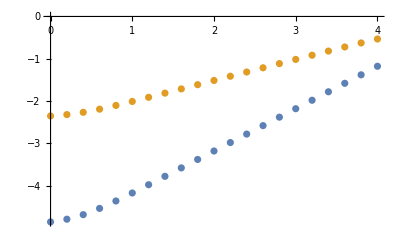

```mathematica
{θboundsTEXONO,ϵboundsTEXONO}//ListPlot
```

```mathematica
Export["data/TEXONO_theta.dat",θboundsTEXONO]
Export["data/TEXONO_epsilon.dat",ϵboundsTEXONO]
```

data/TEXONO_theta.dat

data/TEXONO_epsilon.dat

```mathematica
QeR=0;
QνL= QeL=-1;
sig=√2.71;
gboundsTEXONO=Table[mzpout=mzp;{mzp/MeV,
froot[(chi2[{mzp,#,0,0}]-chi20-sig^2)&,{0,1}]}//Log10,{mzp,1.0mzplist}];//Timing
```

{19.2953,Null}

```mathematica
(*gboundsTEXONO//ListPlot*)
Export["data/TEXONO_gU1L.dat",gboundsTEXONO]
```

data/TEXONO_gU1L.dat

```mathematica
QeR=-1;
QνL= QeL=-3/2;
sig=√2.71;
gboundsTEXONO=Table[mzpout=mzp;{mzp/MeV,
froot[(chi2[{mzp,#,0,0}]-chi20-sig^2)&,{0,1}]}//Log10,{mzp,1.0mzplist}];//Timing

Export["data/TEXONO_gU1X.dat",gboundsTEXONO]
```

{20.5374,Null}

data/TEXONO_gU1X.dat

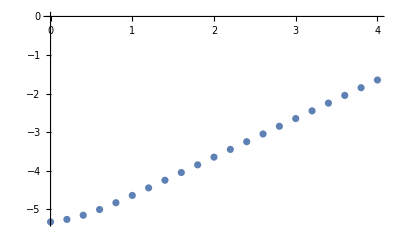

```mathematica
gboundsTEXONO//ListPlot
```

```mathematica
QeR=-1;
QνL= QeL=-1;
sig=√2.71;
sθgboundsTEXONO=Table[mzpout=mzp;
{mzp/MeV,
froot[(chi2[{mzp,0.01#,0,#}]-chi20-sig^2)&,{0,1}],
froot[(chi2[{mzp,1#,0,#}]-chi20-sig^2)&,{0,1}],
froot[(chi2[{mzp,10#,0,#}]-chi20-sig^2)&,{0,1}]
}//Log10,{mzp,1.0mzplist}];//Timing
```

{57.473,Null}

```mathematica
Export["data/TEXONO_theta_B_L.dat",sθgboundsTEXONO]
```

data/TEXONO_theta_B_L.dat

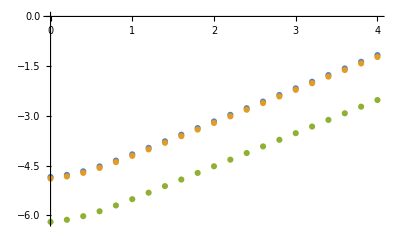

```mathematica
ListPlot[{sθgboundsTEXONO⟦All,{1,2}⟧,sθgboundsTEXONO⟦All,{1,3}⟧,sθgboundsTEXONO⟦All,{1,4}⟧}]
```

## Short for Functions

```mathematica
mf=MatrixForm;
tf=TraditionalForm;
sf=StandardForm;

lsp=ListPlot;

tbl=Table;
err=Interrupt;
fsp=FullSimplify;
iden=IdentityMatrix;
dim=Dimensions;

print=Print;

divide[x1_,x2_,n_]:=Module[{ans},ans=Range[x1,x2,(x2-x1)/n];If[Length[ans]≠ n+1,err[]];
ans
]
```

## Import Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/xj/Dropbox/mywork/P2/code

## many analytical expressions

```mathematica
myGpApprox=GpSM-(2 √2 Gf ((*cα^2 g^2 sw^2+*)B cα sα+A sα^2))/g^2+(A cα^2-B cα sα+g^2 sw^2 sα^2)/(2 cw^2 χzp);
myGmApprox=GmSM-(2 √2 Gf ((*cα^2 g^2 (-1/2+sw^2)+*)cα G sα+H sα^2))/g^2+(cα^2 H-cα G sα+g^2 (-1/2+sw^2) sα^2)/(2 cw^2 χzp);

SMrep={GpSM-> -2 √2 Gf cα^2  sw^2,GmSM-> -2 √2 Gf cα^2  (-1/2+sw^2)
(*,GmSM-> √2 Gf (cα^2  (1-2 sw^2)-2)*)};

HGrep={H-> ((-cw gx QeL-g sw ϵ) (cw gx QνL+g sw ϵ))/(2 (-1+ϵ^2)),
G->  (g  (cw gx (QeL-QνL+2 QνL sw^2)+2 g sw^3 ϵ) √(1-ϵ^2))/(2 (-1+ϵ^2))};
ABrep={A-> 1/(2(1-ϵ^2))(cw^2 gx^2 QeR QνL+cw g gx (QeR+2 QνL) sw ϵ+2 g^2 sw^2 ϵ^2),
B-> 1/(2(1-ϵ^2))(-cw g gx (QeR+2 QνL sw^2) √(1-ϵ^2)-2 g^2 sw ϵ √(1-ϵ^2)-2 g^2 sw^3 ϵ √(1-ϵ^2))};
```

```mathematica
cutExact[x_]:=Exp[Rationalize[Log[x],10^-6]];
Clear[Iij]
Iij[{T1x_,T2x_?NumericQ,Enx_?NumericQ,mx_,Mx_,Gfx_}]:=Module[{T1,T2,En,m,M,Gf},
{T1,T2,En,m,M,Gf}=cutExact[{T1x,T2x,Enx,mx,Mx,Gfx}];
If[T1<T2,
N[({{-(M (T1-T2) (3 En^2+T1^2+T1 T2+T2^2-3 En (T1+T2)))/(12 En^2 π), (M^2 (T1-T2) (T1+T2))/(8 En^2 π), (2 M (m^2+M (4 En-T1-T2)) (T1-T2)+(m^2+2 En M)^2 Log[(m^2+2 M T2)/(m^2+2 M T1)])/(16 En^2 Gf M^2 π), -(M (-T1+T2)+m^2 ArcTanh[(M (T1-T2))/(m^2+M (T1+T2))])/(8 En^2 Gf π)}, {0, (M (-T1+T2))/(4 π), -(M (-T1+T2)+m^2 ArcTanh[(M (T1-T2))/(m^2+M (T1+T2))])/(8 En^2 Gf π), Log[(m^2+2 M T2)/(m^2+2 M T1)]/(4 Gf π)}, {0, 0, -((M (T1-T2) (m^4+m^2 M (2 En+T1+T2)+2 M^2 (En^2+T1 T2)))/((m^2+2 M T1) (m^2+2 M T2))+1/2 (m^2+2 En M) Log[(m^2+2 M T2)/(m^2+2 M T1)])/(8 En^2 Gf^2 M^2 π), -(m^2 (-1/(m^2+2 M T1)+1/(m^2+2 M T2))-Log[m^2+2 M T1]+Log[m^2+2 M T2])/(16 En^2 Gf^2 π)}, {0, 0, 0, (M (-T1+T2))/(4 Gf^2 π (m^2+2 M T1) (m^2+2 M T2))}})
,20],
err[];ConstantArray[0,{4,4}]
]
];
```